# Eigenvalues and Eigenvectors

Aaron Lopes

The word eigenvalue is German in origin, invented by German mathematician David Hilbert. In his paper titled

```mathematica
TextTranslation["Grundzüge einer allgemeinen Theorie der linearen Integralgleichungen"]
```

Main features of a general theory of linear integral equations

in which he was, as the title suggests, attempting to provide a general theory for a system of linear equations. This is not to suggest that eigenvalues were unused before Hilbert; Euler, LaGrange, Cauchy, Fourier, and many others all utilized the eigenvalue and attempted to classify its purpose. The term

```mathematica
WordTranslation["eigen","German"->"English"]
```

{own,very own}

was prefixed to enunciate the importance of the way this value was integral to the nature of a specific transformation.

#### Definition of the Eigenvalue

Suppose we want to linearly transform n vectors. These vectors would form an n x  n matrix

```mathematica
(*For computations, assume n = 2*)
```

```mathematica
(m1 = IdentityMatrix[2])//MatrixForm
```

(1 | 0
0 | 1)

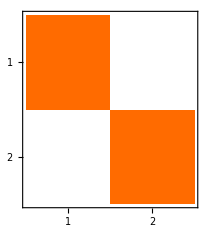

```mathematica
MatrixPlot[m1]
```

```mathematica
(m2 = RandomReal[10,{2,2}]) //MatrixForm
```

(8.69682 | 0.053518
7.0804 | 2.231)

```mathematica
MatrixPlot[m2]
```

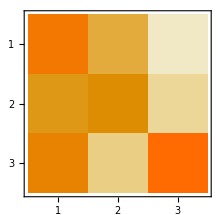

```mathematica
c = CharacteristicPolynomial[m2,x]
```

5.01498-12.2163 x+6.91859 x^2-x^3

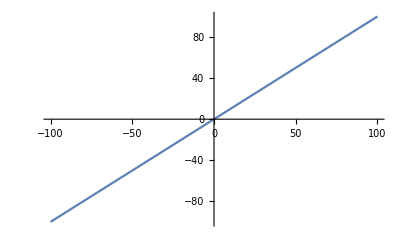

```mathematica
Plot[c, {c,-100,100}]
```

#### Definition of the Gradient

```mathematica
Clear[f,g,x,y]
```

```mathematica
f[x] = x^2
```

x^2

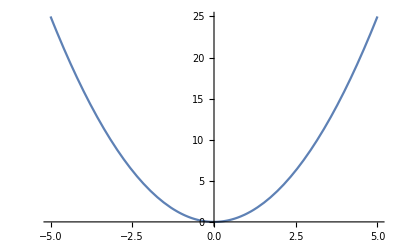

```mathematica
Plot[f[x], {x,-5,5}]
```

```mathematica
g[x,y] = x^2-y^2
```

x^2-y^2

```mathematica
grad= Grad[g[x,y], {x,y}]
```

{2 x,-2 y}

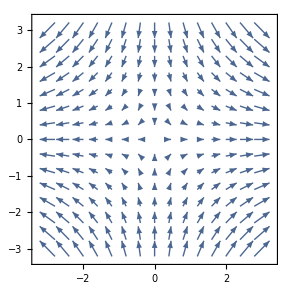

```mathematica
VectorPlot[grad, {x, -3, 3}, {y,-3,3}]
```

```mathematica
Plot3D[g[x,y],{x,-3,3},{y, -3,3}, ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Clear[ex]
ex={{0,1,0},{0,0,1},{1,0,0}}
```

{{0,1,0},{0,0,1},{1,0,0}}

```mathematica
MatrixForm[ex]
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)



```mathematica
AdjacencyGraph[ex]
```

```mathematica
Clear[X,x,y,t]
```

```mathematica
c = {{1,1}, {-2,-1}}
```

```mathematica
MatrixForm[c]
```

(1 | 1
-2 | -1)

```mathematica
Eigenvalues[c]
```

{ⅈ,-ⅈ}

```mathematica
X[t_] = {x[t],y[t]};
```

```mathematica
system = X'[t] == c.X[t]
```

{x'[t],y'[t]}=={x[t]+y[t],-2 x[t]-y[t]}

```mathematica
(*Above defines system of equations*)
```

```mathematica
sol = DSolve[system, {x,y},t]
```

{{x→Function[{t},C[2] Sin[t]+C[1] (Cos[t]+Sin[t])],y→Function[{t},C[2] (Cos[t]-Sin[t])-2 C[1] Sin[t]]}}

```mathematica
particularsols=Partition[Flatten[Table[{x[t],y[t]}/.sol/.{C[1]->1/i,C[2]->1/j},{i,-20,20,6},{j,-20,20,6}]],2];
```

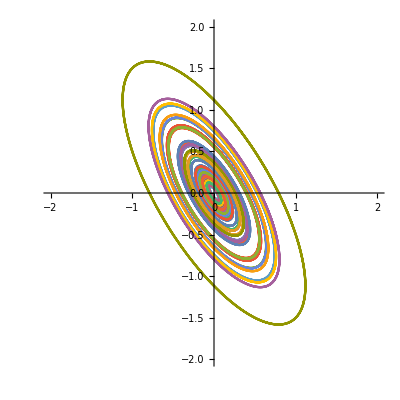

```mathematica
ParametricPlot[Evaluate[particularsols],{t,-10,10}, PlotRange->{-2,2}]
```